```mathematica
"3.1.5.в Формула средних прямоугольников"
```

```mathematica
f[x_]:=1/(1+x)
```

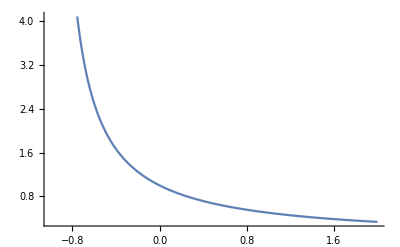

```mathematica
Plot[f[z],{z,-1,2}]
```

```mathematica
x=Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
y=Table[f[x[[i]]],{i,1,Length@x}]
```

{1.,0.909091,0.833333,0.769231,0.714286,0.666667,0.625,0.588235,0.555556,0.526316,0.5}

```mathematica
n=Length@x;
a=x[[1]];
b=x[[Length@x]];
```

```mathematica
(b-a)/n Sum[y[[i]],{i,1,n}] (*формула средних прямоугольников*)
```

0.698883

```mathematica
NIntegrate[f[z],{z,0,1}] (*проверка встроенным оператором*)
```

0.693147

```mathematica
((b-a))^2/(2n)Max[Abs[y]] (*оценка погрешности*)
```

0.0454545